```mathematica
SetDirectory[NotebookDirectory[]]
```

/home/andrei/Work/physics/B-physics/BcBcNLO/calc/BcBc/PP/larin/gamma+Z/renorm

```mathematica
PrependTo[$Path,"/home/andrei/Work/physics/B-physics/BcBcNLO/calc/pkg"];
```

```mathematica
<<X`
```

Package-X v1.0.4, by Hiren H. Patel

For more information, see the

```mathematica
NumericQ[r]=True;
```

```mathematica
PackageXSubs={LDot[p3,p3]->m^2,LDot[p4,p4]->m^2,LDot[p3,p4]->s/2-m^2,mc-> r m, mb-> (1-r) m};
```

```mathematica
toABC={pvA[a_,b_]:>A[b],pvB[a_,b_,c___]:>B[c],pvC[a_,b_,c_,d___]:>C[d],pvC0[a__]:>C[a]};
topvABC={A[a_]:>pvA[0,a],B[a__]:>pvB[0,0,a],C[a__]:>pvC[0,0,0,a]};
```

```mathematica
factor=(Exp[EulerGamma] 1/(4 Pi))^-eps
```

ⅇ^(ℽ (-eps)) (4 π)^eps

```mathematica
ff=Gamma[1-2 eps]/(Gamma[1-eps]^2 Gamma[1+eps](4 Pi)^eps I/(16 Pi^2))
```

-(ⅈ (4 π)^(2-eps) 1-2 eps)/((1-eps)^2 eps+1)

```mathematica
invff=1/ff
```

(ⅈ (4 π)^(eps-2) (1-eps)^2 eps+1)/(1-2 eps)

```mathematica
Normal[Series[FullSimplify[1/factor invff],{eps,0,1}]]
```

ⅈ/(16 π^2)

```mathematica
norm=Expand[Normal[Series[FullSimplify[1/factor invff],{eps,0,2}]]/(I/(16 Pi^2))]
```

1-(π^2 eps^2)/12

```mathematica
Fb=(((1-r)^2 m^2)/mmu)^-eps
```

((m^2 (1-r)^2)/mmu)^-eps

```mathematica
Fc=((r^2 m^2)/mmu)^-eps
```

((m^2 r^2)/mmu)^-eps

```mathematica
Fb=Plus@@ Factor[List@@ Normal[Series[Fb,{eps,0,1}]]/.{Log[(m^2 (1-r)^2)/mmu]->Log[m^2/mmu]+ 2 Log[1-r]}]
```

1-eps (log(m^2/mmu)+2 log(1-r))

```mathematica
Fc=Plus@@ Factor[List@@ Normal[Series[Fc,{eps,0,1}]]/.{Log[(m^2 r^2)/mmu]->Log[m^2/mmu]+ 2 Log[r]}]
```

1-eps (log(m^2/mmu)+2 log(r))

```mathematica
A0[m_]:=m^2+m^2/eps+eps*m^2+(eps*m^2*Pi^2)/6+m^2*Log[mmu/m^2]+eps*m^2*Log[mmu/m^2]+(eps*m^2*Log[mmu/m^2]^2)/2
```

```mathematica
F21[z_]:=(1-eps)/(2 (1-2 eps) z)(1+z-(1-z)^(1-2 eps)-2 (1-z)^(1-2 eps) eps (eps PolyLog[1,1,z]+Hui eps^2 Sum[(-2)^(j-k) PolyLog[k,3-k],{k,1,2}]))
```

```mathematica
B0polylog[s_,m1_,m2_]:=Block[{x,y,lam},If[m1≠ 0 && m2≠0,x=m1^2/s;y=m2^2/s;lam=√((1-x-y)^2-4 x y);  mmu^eps(I Pi^(2-eps))/(2 Pi)^(4-2 eps) (-s)^-eps ((Gamma[1-eps]^2 Gamma[eps])/Gamma[2-2 eps] lam^(1- 2 eps)-Gamma[-1+eps] 1/2(1+x-y-lam) (-x)^-eps F21[(1+x-y-lam)^2/(4 x)]-
Gamma[-1+eps] 1/2(1-x+y-lam) (-y)^-eps F21[(1-x+y-lam)^2/(4 y)]),If[m1==0 && m2 ≠ 0,mmu^eps(I Pi^(2-eps))/(2 Pi)^(4-2 eps) m2^(-2 eps) Gamma[1+eps]/(eps (1-eps))F21[s/m2^2],If[m1≠ 0 && m2== 0,mmu^eps(I Pi^(2-eps))/(2 Pi)^(4-2 eps) m1^(-2 eps) Gamma[1+eps]/(eps (1-eps))F21[s/m1^2],If[m1==0 && m2==0,mmu^eps(I Pi^(2-eps))/(2 Pi)^(4-2 eps) (-s)^-eps (Gamma[1-eps]^2 Gamma[eps])/Gamma[2-2 eps]]]]]]
```

```mathematica
DEN[p1+p2,mZ,1]=1/(s-mZ^2);
```

```mathematica
(* DEN[___]:=0 *)
```

```mathematica
<<cross-sectionNLOLarin.res
```

```mathematica
(* X[a_]:=norm *)
```

```mathematica
mc=1.5;mb=4.9;m=mc+mb;r=mc/m;CF=4/3;CA=3;pi=Pi;s=15^2;mt=175;R1=R2=1;nf=6;AL=1/137;mZ=91.2;mW=80.4;cw=mW/mZ;sw=Sqrt[1-cw^2];
```

```mathematica
mc=1.5;mb=4.9;m=mc+mb;r=mc/m;CF=4/3;CA=3;pi=Pi;s=(15)^2;mt=173;fBc=1;R1=R2=√((Pi m)/3) fBc;AL=1/137;mZ=91.2;mW=80.4;cw=mW/mZ;sw=Sqrt[1-cw^2]; nf=6;
```

```mathematica
Sqrt[4 m^2]
```

12.8

```mathematica
(2mc+2 mc)^2
```

36.

```mathematica
pow[a_,b_]:=a^b
```

```mathematica
(* AS=0.3; mmu=(2 m)^2; *)
```

```mathematica
ex[1]=Collect[Expand[crosssection//N],{A[___],B[___],C[___]}]
```

3.73294×10^-12 eps Aconj(1.5) AS^3-(7.15489×10^-16 Aconj(1.5) AS^3)/eps-2.59026×10^-13 Aconj(1.5) AS^3+4.30784×10^-13 eps Aconj(4.9) AS^3+(2.19027×10^-16 Aconj(4.9) AS^3)/eps+5.54519×10^-13 Aconj(4.9) AS^3+3.69656×10^-14 eps Aconj(173.) AS^3+6.69316×10^-15 Aconj(173.) AS^3-5.67738×10^-12 eps Bconj(12.3596,0.,0.) AS^3+1.20313×10^-11 Bconj(12.3596,0.,0.) AS^3-8.03561×10^-13 eps Bconj(12.3596,1.5,1.5) AS^3+(6.37229×10^-15 Bconj(12.3596,1.5,1.5) AS^3)/eps+1.41576×10^-13 Bconj(12.3596,1.5,1.5) AS^3-1.67593×10^-12 eps Bconj(12.3596,4.9,4.9) AS^3-3.25×10^-13 Bconj(12.3596,4.9,4.9) AS^3-1.29863×10^-9 eps Bconj(12.3596,173.,173.) AS^3-2.1835×10^-10 Bconj(12.3596,173.,173.) AS^3+3.09279×10^-11 eps Bconj(51.9348,1.5,4.9) AS^3-(8.19678×10^-15 Bconj(51.9348,1.5,4.9) AS^3)/eps-7.36281×10^-13 Bconj(51.9348,1.5,4.9) AS^3-3.10928×10^-11 eps Bconj(51.9348,4.9,1.5) AS^3-(8.19678×10^-15 Bconj(51.9348,4.9,1.5) AS^3)/eps-8.14915×10^-14 Bconj(51.9348,4.9,1.5) AS^3-2.69311×10^-11 eps Bconj(76.7444,0.,4.9) AS^3-4.70052×10^-12 Bconj(76.7444,0.,4.9) AS^3+2.26446×10^-11 eps Bconj(76.7444,4.9,0.) AS^3-1.79924×10^-11 Bconj(76.7444,4.9,0.) AS^3-9.69321×10^-12 eps Bconj(131.891,0.,0.) AS^3+8.62855×10^-12 Bconj(131.891,0.,0.) AS^3-1.00923×10^-12 eps Bconj(131.891,1.5,1.5) AS^3+9.63286×10^-13 Bconj(131.891,1.5,1.5) AS^3+9.04313×10^-14 eps Bconj(131.891,4.9,4.9) AS^3+(6.37229×10^-15 Bconj(131.891,4.9,4.9) AS^3)/eps+7.17951×10^-13 Bconj(131.891,4.9,4.9) AS^3-8.30885×10^-12 eps Bconj(131.891,173.,173.) AS^3+1.80248×10^-11 Bconj(131.891,173.,173.) AS^3+3.46295×10^-11 eps Bconj(174.516,0.,1.5) AS^3-2.5454×10^-11 Bconj(174.516,0.,1.5) AS^3-1.23019×10^-11 eps Bconj(174.516,1.5,0.) AS^3+5.39828×10^-12 Bconj(174.516,1.5,0.) AS^3-1.22788×10^-11 eps Bconj(225.,1.5,1.5) AS^3+1.06085×10^-11 Bconj(225.,1.5,1.5) AS^3+1.11926×10^-11 eps Bconj(225.,4.9,4.9) AS^3-6.9485×10^-13 Bconj(225.,4.9,4.9) AS^3+1.64995×10^-11 eps Cconj(2.25,12.3596,2.25,0.,1.5,0.) AS^3-1.05265×10^-11 Cconj(2.25,12.3596,2.25,0.,1.5,0.) AS^3-2.12545×10^-10 eps Cconj(2.25,76.7444,40.96,4.9,1.5,0.) AS^3+1.17993×10^-10 Cconj(2.25,76.7444,40.96,4.9,1.5,0.) AS^3-4.7417×10^-12 eps Cconj(2.25,76.7444,51.9348,4.9,1.5,0.) AS^3+8.98109×10^-13 Cconj(2.25,76.7444,51.9348,4.9,1.5,0.) AS^3-1.94618×10^-10 eps Cconj(2.25,131.891,174.516,0.,1.5,0.) AS^3+1.02626×10^-10 Cconj(2.25,131.891,174.516,0.,1.5,0.) AS^3+1.15503×10^-11 eps Cconj(2.25,174.516,131.891,1.5,1.5,0.) AS^3-1.0263×10^-11 Cconj(2.25,174.516,131.891,1.5,1.5,0.) AS^3-2.08645×10^-10 eps Cconj(2.25,174.516,225.,1.5,1.5,0.) AS^3+1.75156×10^-10 Cconj(2.25,174.516,225.,1.5,1.5,0.) AS^3+1.93563×10^-10 eps Cconj(24.01,12.3596,76.7444,0.,4.9,0.) AS^3-1.27116×10^-10 Cconj(24.01,12.3596,76.7444,0.,4.9,0.) AS^3+1.54896×10^-11 eps Cconj(24.01,76.7444,12.3596,4.9,4.9,0.) AS^3+2.93306×10^-12 Cconj(24.01,76.7444,12.3596,4.9,4.9,0.) AS^3-3.58658×10^-11 eps Cconj(24.01,76.7444,225.,4.9,4.9,0.) AS^3-2.07895×10^-10 Cconj(24.01,76.7444,225.,4.9,4.9,0.) AS^3-5.24155×10^-10 eps Cconj(24.01,131.891,24.01,0.,4.9,0.) AS^3+2.40958×10^-10 Cconj(24.01,131.891,24.01,0.,4.9,0.) AS^3+6.71329×10^-10 eps Cconj(24.01,174.516,40.96,1.5,4.9,0.) AS^3-3.28923×10^-10 Cconj(24.01,174.516,40.96,1.5,4.9,0.) AS^3-3.7731×10^-11 eps Cconj(24.01,174.516,51.9348,1.5,4.9,0.) AS^3+4.03325×10^-11 Cconj(24.01,174.516,51.9348,1.5,4.9,0.) AS^3+4.50458×10^-11 eps Cconj(51.9348,51.9348,225.,1.5,1.5,4.9) AS^3-4.60809×10^-11 Cconj(51.9348,51.9348,225.,1.5,1.5,4.9) AS^3-4.7417×10^-12 eps Cconj(76.7444,2.25,51.9348,1.5,4.9,0.) AS^3+8.98109×10^-13 Cconj(76.7444,2.25,51.9348,1.5,4.9,0.) AS^3-4.64205×10^-11 eps Cconj(76.7444,12.3596,24.01,0.,4.9,0.) AS^3-1.39449×10^-10 Cconj(76.7444,12.3596,24.01,0.,4.9,0.) AS^3+1.54896×10^-11 eps Cconj(76.7444,24.01,12.3596,4.9,4.9,0.) AS^3+2.93306×10^-12 Cconj(76.7444,24.01,12.3596,4.9,4.9,0.) AS^3+2.9375×10^-10 eps Cconj(76.7444,24.01,225.,4.9,4.9,0.) AS^3+2.30169×10^-10 Cconj(76.7444,24.01,225.,4.9,4.9,0.) AS^3+1.15503×10^-11 eps Cconj(174.516,2.25,131.891,1.5,1.5,0.) AS^3-1.0263×10^-11 Cconj(174.516,2.25,131.891,1.5,1.5,0.) AS^3-3.7731×10^-11 eps Cconj(174.516,24.01,51.9348,4.9,1.5,0.) AS^3+4.03325×10^-11 Cconj(174.516,24.01,51.9348,4.9,1.5,0.) AS^3+1.97768×10^-10 eps Cconj(174.516,131.891,2.25,0.,1.5,0.) AS^3-1.60664×10^-10 Cconj(174.516,131.891,2.25,0.,1.5,0.) AS^3+7.93695×10^-11 eps Cconj(225.,51.9348,51.9348,1.5,4.9,4.9) AS^3-6.20782×10^-12 Cconj(225.,51.9348,51.9348,1.5,4.9,4.9) AS^3+1.6555×10^-13 log(0.234375) AS^3+4.51335×10^-12 log(0.765625) AS^3-2.33945×10^-12 log(0.0244141 mmu) AS^3-(2.45385×10^-12 AS^3)/eps-1.84536×10^-11 AS^3+1.02687×10^-13 AS^2+(3.73294×10^-12 eps AS^3-(7.15489×10^-16 AS^3)/eps-2.59026×10^-13 AS^3) A(1.5)+(4.30784×10^-13 eps AS^3+(2.19027×10^-16 AS^3)/eps+5.54519×10^-13 AS^3) A(4.9)+(3.69656×10^-14 eps AS^3+6.69316×10^-15 AS^3) A(173.)+(1.20313×10^-11 AS^3-5.67738×10^-12 AS^3 eps) B(12.3596,0.,0.)+(-8.03561×10^-13 eps AS^3+(6.37229×10^-15 AS^3)/eps+1.41576×10^-13 AS^3) B(12.3596,1.5,1.5)+(-1.67593×10^-12 eps AS^3-3.25×10^-13 AS^3) B(12.3596,4.9,4.9)+(-1.29863×10^-9 eps AS^3-2.1835×10^-10 AS^3) B(12.3596,173.,173.)+(3.09279×10^-11 eps AS^3-(8.19678×10^-15 AS^3)/eps-7.36281×10^-13 AS^3) B(51.9348,1.5,4.9)+(-3.10928×10^-11 eps AS^3-(8.19678×10^-15 AS^3)/eps-8.14915×10^-14 AS^3) B(51.9348,4.9,1.5)+(-2.69311×10^-11 eps AS^3-4.70052×10^-12 AS^3) B(76.7444,0.,4.9)+(2.26446×10^-11 AS^3 eps-1.79924×10^-11 AS^3) B(76.7444,4.9,0.)+(8.62855×10^-12 AS^3-9.69321×10^-12 AS^3 eps) B(131.891,0.,0.)+(9.63286×10^-13 AS^3-1.00923×10^-12 AS^3 eps) B(131.891,1.5,1.5)+(9.04313×10^-14 eps AS^3+(6.37229×10^-15 AS^3)/eps+7.17951×10^-13 AS^3) B(131.891,4.9,4.9)+(1.80248×10^-11 AS^3-8.30885×10^-12 AS^3 eps) B(131.891,173.,173.)+(3.46295×10^-11 AS^3 eps-2.5454×10^-11 AS^3) B(174.516,0.,1.5)+(5.39828×10^-12 AS^3-1.23019×10^-11 AS^3 eps) B(174.516,1.5,0.)+(1.06085×10^-11 AS^3-1.22788×10^-11 AS^3 eps) B(225.,1.5,1.5)+(1.11926×10^-11 AS^3 eps-6.9485×10^-13 AS^3) B(225.,4.9,4.9)+(1.64995×10^-11 AS^3 eps-1.05265×10^-11 AS^3) C[2.25,12.3596,2.25,0,1.5,0]+(1.17993×10^-10 AS^3-2.12545×10^-10 AS^3 eps) C[2.25,76.7444,40.96,4.9,1.5,0]+(8.98109×10^-13 AS^3-4.7417×10^-12 AS^3 eps) C[2.25,76.7444,51.9348,4.9,1.5,0]+(1.02626×10^-10 AS^3-1.94618×10^-10 AS^3 eps) C[2.25,131.891,174.516,0,1.5,0]+(1.15503×10^-11 AS^3 eps-1.0263×10^-11 AS^3) C[2.25,174.516,131.891,1.5,1.5,0]+(1.75156×10^-10 AS^3-2.08645×10^-10 AS^3 eps) C[2.25,174.516,225,1.5,1.5,0]+(1.93563×10^-10 AS^3 eps-1.27116×10^-10 AS^3) C[24.01,12.3596,76.7444,0,4.9,0]+(1.54896×10^-11 eps AS^3+2.93306×10^-12 AS^3) C[24.01,76.7444,12.3596,4.9,4.9,0]+(-3.58658×10^-11 eps AS^3-2.07895×10^-10 AS^3) C[24.01,76.7444,225,4.9,4.9,0]+(2.40958×10^-10 AS^3-5.24155×10^-10 AS^3 eps) C[24.01,131.891,24.01,0,4.9,0]+(6.71329×10^-10 AS^3 eps-3.28923×10^-10 AS^3) C[24.01,174.516,40.96,1.5,4.9,0]+(4.03325×10^-11 AS^3-3.7731×10^-11 AS^3 eps) C[24.01,174.516,51.9348,1.5,4.9,0]+(4.50458×10^-11 AS^3 eps-4.60809×10^-11 AS^3) C[51.9348,51.9348,225,1.5,1.5,4.9]+(8.98109×10^-13 AS^3-4.7417×10^-12 AS^3 eps) C[76.7444,2.25,51.9348,1.5,4.9,0]+(-4.64205×10^-11 eps AS^3-1.39449×10^-10 AS^3) C[76.7444,12.3596,24.01,0,4.9,0]+(1.54896×10^-11 eps AS^3+2.93306×10^-12 AS^3) C[76.7444,24.01,12.3596,4.9,4.9,0]+(2.9375×10^-10 eps AS^3+2.30169×10^-10 AS^3) C[76.7444,24.01,225,4.9,4.9,0]+(1.15503×10^-11 AS^3 eps-1.0263×10^-11 AS^3) C[174.516,2.25,131.891,1.5,1.5,0]+(4.03325×10^-11 AS^3-3.7731×10^-11 AS^3 eps) C[174.516,24.01,51.9348,4.9,1.5,0]+(1.97768×10^-10 AS^3 eps-1.60664×10^-10 AS^3) C[174.516,131.891,2.25,0,1.5,0]+(7.93695×10^-11 AS^3 eps-6.20782×10^-12 AS^3) C[225,51.9348,51.9348,1.5,4.9,4.9]

```mathematica
Bconj[s,0.,0.]/.{Bconj[s_,0.,0.]:> Expand[ExpandAll[Conjugate[FullSimplify[Normal[Series[ff B0polylog[s+0.00000001 I,0,0] ,{eps,0,1}]]]]]/.{Conjugate[eps]-> eps,Conjugate[Log[mmu]]-> Log[mmu],Conjugate[eps Log[mmu]]-> eps Log[mmu]}]}
```

-(3.4161+3.14159 ⅈ) eps log(mmu)+(2.90007+10.732 ⅈ) eps-(3.4161+3.14159 ⅈ)+0.5 eps log^2(mmu)+1/eps+log(mmu)

```mathematica
ex[2]=Expand[Simplify[Normal[Series[ex[1]/.{A[m_]:> A0[m],B[s_,0.,0.]:> FullSimplify[Normal[Series[ff B0polylog[s+0.00000001 I,0,0] ,{eps,0,1}]]],B[s_,m_,0.]:> FullSimplify[Normal[Series[ff B0polylog[s+0.00000001 I,m,0] ,{eps,0,1}]]],B[s_,0.,m_]:> FullSimplify[Normal[Series[ff B0polylog[s+0.00000001 I,0,m] ,{eps,0,1}]]],B[s_,m1_,m2_]:> FullSimplify[Normal[Series[ff B0polylog[s+0.00000001 I,m1,m2] ,{eps,0,1}]]],Aconj[m_]:> Conjugate[A0[m]],Bconj[s_,0.,0.]:> Conjugate[FullSimplify[Normal[Series[ff B0polylog[s+0.00000001 I,0,0] ,{eps,0,1}]]]],Bconj[s_,m_,0.]:> Conjugate[FullSimplify[Normal[Series[ff B0polylog[s+0.00000001 I,m,0] ,{eps,0,1}]]]],Bconj[s_,0.,m_]:> Conjugate[FullSimplify[Normal[Series[ff B0polylog[s+0.00000001 I,0,m] ,{eps,0,1}]]]],Bconj[s_,m1_,m2_]:> Conjugate[FullSimplify[Normal[Series[ff B0polylog[s+0.00000001 I,m1,m2] ,{eps,0,1}]]]],log[a_]:>  Log[a]},{eps,0,0}]]/.{Log[a_ mmu]-> Log[a]+Log[mmu]}]/.{Conjugate[eps]-> eps,Conjugate[Log[mmu]]-> Log[mmu],Conjugate[eps Log[mmu]]-> eps Log[mmu]}]
```

(-2.11909×10^-8+4.66781×10^-11 ⅈ) eps^2 AS^3-(9.19186×10^-11-1.54046×10^-26 ⅈ) eps^2 log^2(mmu) AS^3+(1.23057×10^-12+1.45713×10^-28 ⅈ) eps log^2(mmu) AS^3-(1.32325×10^-24+1.0376×10^-34 ⅈ) log^2(mmu) AS^3+(2.5877×10^-9-2.58494×10^-26 ⅈ) eps AS^3+1.64995×10^-11 eps C[2.25,12.3596,2.25,0,1.5,0] AS^3-(1.05265×10^-11-3.15544×10^-30 ⅈ) C[2.25,12.3596,2.25,0,1.5,0] AS^3-(2.12545×10^-10-7.57306×10^-29 ⅈ) eps C[2.25,76.7444,40.96,4.9,1.5,0] AS^3+(1.17993×10^-10-8.20415×10^-29 ⅈ) C[2.25,76.7444,40.96,4.9,1.5,0] AS^3-(4.7417×10^-12-6.90253×10^-30 ⅈ) eps C[2.25,76.7444,51.9348,4.9,1.5,0] AS^3+(8.98109×10^-13+9.86076×10^-32 ⅈ) C[2.25,76.7444,51.9348,4.9,1.5,0] AS^3-(1.94618×10^-10+1.32529×10^-28 ⅈ) eps C[2.25,131.891,174.516,0,1.5,0] AS^3+(1.02626×10^-10-2.08259×10^-28 ⅈ) C[2.25,131.891,174.516,0,1.5,0] AS^3+(1.15503×10^-11-3.9443×10^-30 ⅈ) eps C[2.25,174.516,131.891,1.5,1.5,0] AS^3-(1.0263×10^-11-7.09975×10^-30 ⅈ) C[2.25,174.516,131.891,1.5,1.5,0] AS^3-(2.08645×10^-10-5.6798×10^-28 ⅈ) eps C[2.25,174.516,225,1.5,1.5,0] AS^3+(1.75156×10^-10-6.31089×10^-29 ⅈ) C[2.25,174.516,225,1.5,1.5,0] AS^3+(1.93563×10^-10-4.41762×10^-28 ⅈ) eps C[24.01,12.3596,76.7444,0,4.9,0] AS^3-(1.27116×10^-10-1.64083×10^-28 ⅈ) C[24.01,12.3596,76.7444,0,4.9,0] AS^3+(1.54896×10^-11-6.31089×10^-30 ⅈ) eps C[24.01,76.7444,12.3596,4.9,4.9,0] AS^3+(2.93306×10^-12+3.45127×10^-30 ⅈ) C[24.01,76.7444,12.3596,4.9,4.9,0] AS^3-(3.58658×10^-11-3.78653×10^-29 ⅈ) eps C[24.01,76.7444,225,4.9,4.9,0] AS^3-(2.07895×10^-10-2.1457×10^-28 ⅈ) C[24.01,76.7444,225,4.9,4.9,0] AS^3-(5.24155×10^-10-3.28166×10^-28 ⅈ) eps C[24.01,131.891,24.01,0,4.9,0] AS^3+(2.40958×10^-10-2.01948×10^-28 ⅈ) C[24.01,131.891,24.01,0,4.9,0] AS^3+(6.71329×10^-10-1.00974×10^-28 ⅈ) eps C[24.01,174.516,40.96,1.5,4.9,0] AS^3-(3.28923×10^-10-4.41762×10^-28 ⅈ) C[24.01,174.516,40.96,1.5,4.9,0] AS^3-(3.7731×10^-11-6.7842×10^-29 ⅈ) eps C[24.01,174.516,51.9348,1.5,4.9,0] AS^3+(4.03325×10^-11-2.99767×10^-29 ⅈ) C[24.01,174.516,51.9348,1.5,4.9,0] AS^3+(4.50458×10^-11+1.57772×10^-30 ⅈ) eps C[51.9348,51.9348,225,1.5,1.5,4.9] AS^3-(4.60809×10^-11-5.52203×10^-29 ⅈ) C[51.9348,51.9348,225,1.5,1.5,4.9] AS^3-(4.7417×10^-12-6.90253×10^-30 ⅈ) eps C[76.7444,2.25,51.9348,1.5,4.9,0] AS^3+(8.98109×10^-13+9.86076×10^-32 ⅈ) C[76.7444,2.25,51.9348,1.5,4.9,0] AS^3-(4.64205×10^-11-1.10441×10^-29 ⅈ) eps C[76.7444,12.3596,24.01,0,4.9,0] AS^3-(1.39449×10^-10-2.39814×10^-28 ⅈ) C[76.7444,12.3596,24.01,0,4.9,0] AS^3+(1.54896×10^-11-6.31089×10^-30 ⅈ) eps C[76.7444,24.01,12.3596,4.9,4.9,0] AS^3+(2.93306×10^-12+3.45127×10^-30 ⅈ) C[76.7444,24.01,12.3596,4.9,4.9,0] AS^3+(2.9375×10^-10-4.41762×10^-28 ⅈ) eps C[76.7444,24.01,225,4.9,4.9,0] AS^3+(2.30169×10^-10-1.00974×10^-28 ⅈ) C[76.7444,24.01,225,4.9,4.9,0] AS^3+(1.15503×10^-11-3.9443×10^-30 ⅈ) eps C[174.516,2.25,131.891,1.5,1.5,0] AS^3-(1.0263×10^-11-7.09975×10^-30 ⅈ) C[174.516,2.25,131.891,1.5,1.5,0] AS^3-(3.7731×10^-11-6.7842×10^-29 ⅈ) eps C[174.516,24.01,51.9348,4.9,1.5,0] AS^3+(4.03325×10^-11-2.99767×10^-29 ⅈ) C[174.516,24.01,51.9348,4.9,1.5,0] AS^3+(1.97768×10^-10-1.26218×10^-29 ⅈ) eps C[174.516,131.891,2.25,0,1.5,0] AS^3-(1.60664×10^-10-2.65057×10^-28 ⅈ) C[174.516,131.891,2.25,0,1.5,0] AS^3+(7.93695×10^-11-6.31089×10^-30 ⅈ) eps C[225,51.9348,51.9348,1.5,4.9,4.9] AS^3-(6.20782×10^-12+1.97215×10^-30 ⅈ) C[225,51.9348,51.9348,1.5,4.9,4.9] AS^3+1.64995×10^-11 eps Cconj(2.25,12.3596,2.25,0.,1.5,0.) AS^3-(1.05265×10^-11-3.15544×10^-30 ⅈ) Cconj(2.25,12.3596,2.25,0.,1.5,0.) AS^3-(2.12545×10^-10-7.57306×10^-29 ⅈ) eps Cconj(2.25,76.7444,40.96,4.9,1.5,0.) AS^3+(1.17993×10^-10-8.20415×10^-29 ⅈ) Cconj(2.25,76.7444,40.96,4.9,1.5,0.) AS^3-(4.7417×10^-12-6.90253×10^-30 ⅈ) eps Cconj(2.25,76.7444,51.9348,4.9,1.5,0.) AS^3+(8.98109×10^-13+9.86076×10^-32 ⅈ) Cconj(2.25,76.7444,51.9348,4.9,1.5,0.) AS^3-(1.94618×10^-10+1.32529×10^-28 ⅈ) eps Cconj(2.25,131.891,174.516,0.,1.5,0.) AS^3+(1.02626×10^-10-2.08259×10^-28 ⅈ) Cconj(2.25,131.891,174.516,0.,1.5,0.) AS^3+(1.15503×10^-11-3.9443×10^-30 ⅈ) eps Cconj(2.25,174.516,131.891,1.5,1.5,0.) AS^3-(1.0263×10^-11-7.09975×10^-30 ⅈ) Cconj(2.25,174.516,131.891,1.5,1.5,0.) AS^3-(2.08645×10^-10-5.6798×10^-28 ⅈ) eps Cconj(2.25,174.516,225.,1.5,1.5,0.) AS^3+(1.75156×10^-10-6.31089×10^-29 ⅈ) Cconj(2.25,174.516,225.,1.5,1.5,0.) AS^3+(1.93563×10^-10-4.41762×10^-28 ⅈ) eps Cconj(24.01,12.3596,76.7444,0.,4.9,0.) AS^3-(1.27116×10^-10-1.64083×10^-28 ⅈ) Cconj(24.01,12.3596,76.7444,0.,4.9,0.) AS^3+(1.54896×10^-11-6.31089×10^-30 ⅈ) eps Cconj(24.01,76.7444,12.3596,4.9,4.9,0.) AS^3+(2.93306×10^-12+3.45127×10^-30 ⅈ) Cconj(24.01,76.7444,12.3596,4.9,4.9,0.) AS^3-(3.58658×10^-11-3.78653×10^-29 ⅈ) eps Cconj(24.01,76.7444,225.,4.9,4.9,0.) AS^3-(2.07895×10^-10-2.1457×10^-28 ⅈ) Cconj(24.01,76.7444,225.,4.9,4.9,0.) AS^3-(5.24155×10^-10-3.28166×10^-28 ⅈ) eps Cconj(24.01,131.891,24.01,0.,4.9,0.) AS^3+(2.40958×10^-10-2.01948×10^-28 ⅈ) Cconj(24.01,131.891,24.01,0.,4.9,0.) AS^3+(6.71329×10^-10-1.00974×10^-28 ⅈ) eps Cconj(24.01,174.516,40.96,1.5,4.9,0.) AS^3-(3.28923×10^-10-4.41762×10^-28 ⅈ) Cconj(24.01,174.516,40.96,1.5,4.9,0.) AS^3-(3.7731×10^-11-6.7842×10^-29 ⅈ) eps Cconj(24.01,174.516,51.9348,1.5,4.9,0.) AS^3+(4.03325×10^-11-2.99767×10^-29 ⅈ) Cconj(24.01,174.516,51.9348,1.5,4.9,0.) AS^3+(4.50458×10^-11+1.57772×10^-30 ⅈ) eps Cconj(51.9348,51.9348,225.,1.5,1.5,4.9) AS^3-(4.60809×10^-11-5.52203×10^-29 ⅈ) Cconj(51.9348,51.9348,225.,1.5,1.5,4.9) AS^3-(4.7417×10^-12-6.90253×10^-30 ⅈ) eps Cconj(76.7444,2.25,51.9348,1.5,4.9,0.) AS^3+(8.98109×10^-13+9.86076×10^-32 ⅈ) Cconj(76.7444,2.25,51.9348,1.5,4.9,0.) AS^3-(4.64205×10^-11-1.10441×10^-29 ⅈ) eps Cconj(76.7444,12.3596,24.01,0.,4.9,0.) AS^3-(1.39449×10^-10-2.39814×10^-28 ⅈ) Cconj(76.7444,12.3596,24.01,0.,4.9,0.) AS^3+(1.54896×10^-11-6.31089×10^-30 ⅈ) eps Cconj(76.7444,24.01,12.3596,4.9,4.9,0.) AS^3+(2.93306×10^-12+3.45127×10^-30 ⅈ) Cconj(76.7444,24.01,12.3596,4.9,4.9,0.) AS^3+(2.9375×10^-10-4.41762×10^-28 ⅈ) eps Cconj(76.7444,24.01,225.,4.9,4.9,0.) AS^3+(2.30169×10^-10-1.00974×10^-28 ⅈ) Cconj(76.7444,24.01,225.,4.9,4.9,0.) AS^3+(1.15503×10^-11-3.9443×10^-30 ⅈ) eps Cconj(174.516,2.25,131.891,1.5,1.5,0.) AS^3-(1.0263×10^-11-7.09975×10^-30 ⅈ) Cconj(174.516,2.25,131.891,1.5,1.5,0.) AS^3-(3.7731×10^-11-6.7842×10^-29 ⅈ) eps Cconj(174.516,24.01,51.9348,4.9,1.5,0.) AS^3+(4.03325×10^-11-2.99767×10^-29 ⅈ) Cconj(174.516,24.01,51.9348,4.9,1.5,0.) AS^3+(1.97768×10^-10-1.26218×10^-29 ⅈ) eps Cconj(174.516,131.891,2.25,0.,1.5,0.) AS^3-(1.60664×10^-10-2.65057×10^-28 ⅈ) Cconj(174.516,131.891,2.25,0.,1.5,0.) AS^3+(7.93695×10^-11-6.31089×10^-30 ⅈ) eps Cconj(225.,51.9348,51.9348,1.5,4.9,4.9) AS^3-(6.20782×10^-12+1.97215×10^-30 ⅈ) Cconj(225.,51.9348,51.9348,1.5,4.9,4.9) AS^3+(3.14001×10^-9+3.91501×10^-12 ⅈ) eps^2 log(mmu) AS^3+(4.44306×10^-11-1.77715×10^-26 ⅈ) eps log(mmu) AS^3-((2.6465×10^-24-5.33614×10^-42 ⅈ) log(mmu) AS^3)/eps+(1.14402×10^-13-3.10547×10^-30 ⅈ) log(mmu) AS^3+((7.71476×10^-22+4.43734×10^-31 ⅈ) AS^3)/eps-((2.6465×10^-24+1.627×10^-32 ⅈ) AS^3)/eps^2+(3.3234×10^-11-4.96351×10^-27 ⅈ) AS^3+(1.02687×10^-13+6.16298×10^-33 ⅈ) AS^2

```mathematica
ex[3]=Expand[Chop[LoopRefine[Expand[Normal[Series[ex[2],{eps,0,0}]]/.{Cconj[a___]:> Conjugate[C[a]]}]/.topvABC],10^(-20)]]
```

1.14402×10^-13 AS^3 log(mmu)+9.76871×10^-12 AS^3+1.02687×10^-13 AS^2

```mathematica
ex[4]=Collect[Chop[ex[3],10^(-20)],AS]/.{AS-> z *0.3}//Expand
```

3.08885×10^-15 z^3 log(mmu)+2.63755×10^-13 z^3+9.24182×10^-15 z^2

```mathematica
ratioCrossSection[mu2_]:=Abs[N[Coefficient[ex[4],z^3]/Coefficient[ex[4],z^2]/.{mmu-> mu2}]]
```

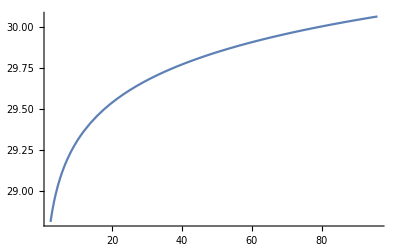

```mathematica
Plot[ratioCrossSection[mmu],{mmu,(mc)^2,(2mb)^2}]
```

```mathematica
ratioCrossSection[(2mc)^2]
```

29.2737

```mathematica
CrossSectionRatio=Abs[N[Coefficient[ex[4],z^3]/Coefficient[ex[4],z^2]]]/.{mmu-> m^2}
```

29.7802

```mathematica
Chop[Expand[ex[4]0.3894 10^12/.{mmu-> (2 mc)^2}],10^(-9)]
```

0.105349 z^3+0.00359876 z^2

```mathematica
Chop[Expand[ex[4]0.3894 10^12/.{mmu-> (2 m)^2}],10^(-9)]
```

0.108839 z^3+0.00359876 z^2

```mathematica
LO 0.3894 10^12/.{AS-> 0.3 z}
```

3.894×10^11 LO

```mathematica
LO=+pow[s,1/2]*pow[s-4*m^2,1/2]*pi*R1^2*R2^2*AL^2*AS^2*(+64/243*m^(-2)*s^(-4)*r^(-4)+256/243*m^(-2)*s^(-4)*r^(-2)+512/243*m^(-2)*s^(-4)*r^(-1)-256/243*s^(-5)*r^(-5)-512/243*s^(-5)*r^(-3)-512/81*s^(-5)*r^(-2)-1024/81*s^(-5)*r^(-1)+256/243*m^2*s^(-6)*r^(-6)+512/243*m^2*s^(-6)*r^(-5)-256/81*m^2*s^(-6)*r^(-4)+2048/243*m^2*s^(-6)*r^(-3)+1024/81*m^2*s^(-6)*r^(-2)+2048/81*m^2*s^(-6)*r^(-1)-1024/243*m^4*s^(-7)*r^(-6)+2048/243*m^4*s^(-7)*r^(-5)-1024/243*m^4*s^(-7)*r^(-4)-4096/243*m^4*s^(-7)*r^(-2)-8192/243*m^4*s^(-7)*r^(-1)+1024/243/(1-6*r+15*r^2-20*r^3+15*r^4-6*r^5+r^6)*m^2*s^(-6)-4096/243/(1-6*r+15*r^2-20*r^3+15*r^4-6*r^5+r^6)*m^4*s^(-7)-1024/243/(1-5*r+10*r^2-10*r^3+5*r^4-r^5)*s^(-5)+2048/243/(1-5*r+10*r^2-10*r^3+5*r^4-r^5)*m^2*s^(-6)+8192/243/(1-5*r+10*r^2-10*r^3+5*r^4-r^5)*m^4*s^(-7)+256/243/(1-4*r+6*r^2-4*r^3+r^4)*m^(-2)*s^(-4)-1024/81/(1-4*r+6*r^2-4*r^3+r^4)*m^2*s^(-6)-4096/243/(1-4*r+6*r^2-4*r^3+r^4)*m^4*s^(-7)-512/243/(1-3*r+3*r^2-r^3)*s^(-5)+2048/243/(1-3*r+3*r^2-r^3)*m^2*s^(-6)+256/243/(1-2*r+r^2)*m^(-2)*s^(-4)-512/81/(1-2*r+r^2)*s^(-5)+1024/81/(1-2*r+r^2)*m^2*s^(-6)-4096/243/(1-2*r+r^2)*m^4*s^(-7)+512/243/(1-r)*m^(-2)*s^(-4)-1024/81/(1-r)*s^(-5)+2048/81/(1-r)*m^2*s^(-6)-8192/243/(1-r)*m^4*s^(-7))
```

1.03842×10^-13 AS^2